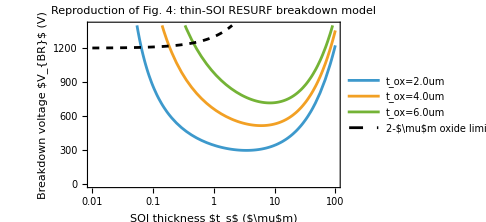

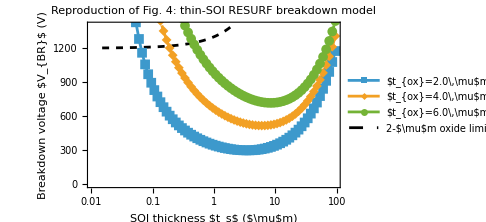

fig4_reproduction.png

fig4_reproduction.png

fig4_reproduction.png

```mathematica
(*Clear definitions first*)ClearAll["Global`*"];

(*Define Constants-renamed to remove underscores*)
aCm=7.03*10^5;
bVcm=1.468*10^6;
umToCm=10^-4;

(*Function to find gamma-using CamelCase names*)
gammaFromTs[tsUm_?NumericQ]:=Module[{ats,gamma},ats=aCm*tsUm*umToCm;
If[ats<=1,Return[Indeterminate]];
gamma/. FindRoot[ats*(Exp[-gamma]-gamma*ExpIntegralE[1,gamma])-1==0,{gamma,1,0.0001,100}]];

(*Breakdown Voltage function*)
breakdownVoltage[tsUm_?NumericQ,toxUm_?NumericQ,epsRatio_:3.0]:=Module[{gamma,tEffCm},gamma=gammaFromTs[tsUm];
tEffCm=(tsUm/2.0+epsRatio*toxUm)*umToCm;
If[NumericQ[gamma],bVcm*tEffCm/gamma,Indeterminate]];

(*Define Oxide Limit*)
oxideLimit[ts_]:=600.0*(2.0+ts/6.0);

(*Generate Plot*)
plot=Plot[{breakdownVoltage[ts,2.0],breakdownVoltage[ts,4.0],breakdownVoltage[ts,6.0],oxideLimit[ts]},{ts,0.01,100},PlotRange->{0,1400},ScalingFunctions->{"Log",None},Frame->True,FrameLabel->{"SOI thickness $t_s$ ($\mu$m)","Breakdown voltage $V_{BR}$ (V)"},PlotStyle->{Automatic,Automatic,Automatic,Directive[Dashed,Black]},PlotLegends->{"t_ox=2.0um","t_ox=4.0um","t_ox=6.0um","2-$\mu$m oxide limit ($E_{ox}=600$ V/$\mu$m)"},PlotLabel->"Reproduction of Fig. 4: thin-SOI RESURF breakdown model",ImageSize->Medium]

(*1. Generate the data points*)
(*Use Logarithmic spacing instead of linear*)tsValues=10^Range[Log10[0.015],Log10[100],0.05];

(*Generate data points*)
data1=Table[{ts,breakdownVoltage[ts,2.0]},{ts,tsValues}];
data2=Table[{ts,breakdownVoltage[ts,4.0]},{ts,tsValues}];
data3=Table[{ts,breakdownVoltage[ts,6.0]},{ts,tsValues}];
limitData=Table[{ts,oxideLimit[ts]},{ts,tsValues}];

(*Plotting code remains the same*)
plot=ListLinePlot[{data1,data2,data3,limitData},PlotRange->{0,1400},ScalingFunctions->{"Log",None},Frame->True,FrameLabel->{"SOI thickness $t_s$ ($\mu$m)","Breakdown voltage $V_{BR}$ (V)"},PlotMarkers->{{"■",10},{"◆",10},{"●",10},None},PlotStyle->{Automatic,Automatic,Automatic,Directive[Dashed,Black]},PlotLegends->{"$t_{ox}=2.0\,\mu$m","$t_{ox}=4.0\,\mu$m","$t_{ox}=6.0\,\mu$m","2-$\mu$m oxide limit ($E_{ox}=600$ V/$\mu$m)"},PlotLabel->"Reproduction of Fig. 4: thin-SOI RESURF breakdown model",ImageSize->Medium]

Export["fig4_reproduction.png",plot,"PNG",ImageResolution->220]

(*Export*)
Export["fig4_reproduction.png",plot,"PNG",ImageResolution->220]

(*Export*)
Export["fig4_reproduction.png",plot,"PNG",ImageResolution->220]
```